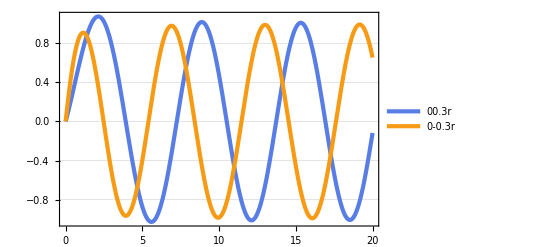

```mathematica
Plot[{CoulombF[0,0.3,r],CoulombF[0,-0.3,r]},{r,0,20},ImageSize->Full,PlotTheme->"Business",PlotLegends->"Expressions"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Regular Coulomb wave function F plotted from 0 to 20 with repulsive and attractive interactions in Mathematica.svg"}],Plot[{CoulombF[0,0.3,r],CoulombF[0,-0.3,r]},{r,0,20},ImageSize->Full,PlotTheme->"Business",PlotLegends->"Expressions"]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\Regular Coulomb wave function F plotted from 0 to 20 with repulsive and attractive interactions in Mathematica.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\Regular Coulomb wave function F plotted from 0 to 20 with repulsive and attractive interactions in Mathematica.svg"]
```

```mathematica
CoulombF
```

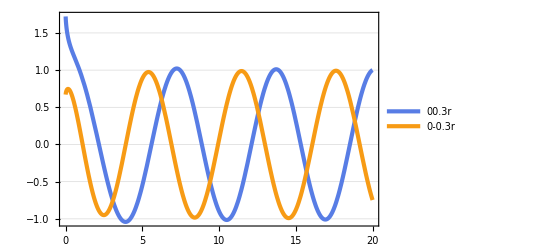

```mathematica
Plot[{CoulombG[0,0.3,r],CoulombG[0,-0.3,r]},{r,0,20},ImageSize->Full,PlotTheme->"Business",PlotLegends->"Expressions"]
```

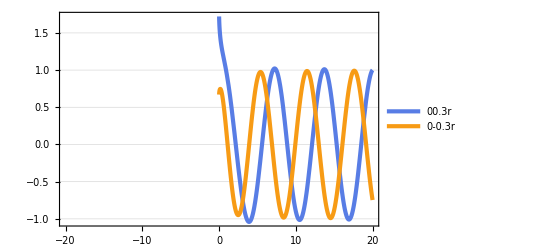

```mathematica
Plot[{CoulombG[0,0.3,r],CoulombG[0,-0.3,r]},{r,-20,20},ImageSize->Full,PlotTheme->"Business",PlotLegends->"Expressions"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Irregular Coulomb wave function G plotted from 0 to 20 with repulsive and attractive interactions in Mathematica.svg"}],Plot[{CoulombG[0,0.3,r],CoulombG[0,-0.3,r]},{r,0,20},ImageSize->Full,PlotTheme->"Business",PlotLegends->"Expressions"]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\Irregular Coulomb wave function G plotted from 0 to 20 with repulsive and attractive interactions in Mathematica.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\Irregular Coulomb wave function G plotted from 0 to 20 with repulsive and attractive interactions in Mathematica.svg"]
```

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\Irregular Coulomb wave function G plotted from 0 to 20 with repulsive and attractive interactions in Mathematica.svg"]
```

```mathematica
FunctionDomain[CoulombG[a,b,c],a]
```

(a∈ℤ&&c<0)||(c≥0&&a≥-1)||c>0

```mathematica
Resolve[((a∈Integers&&c<0)||(c≥0&&a≥-1)||c>0)&&a∈Integers,{c,a}]
```

((a∈ℤ&&c<0)||(c≥0&&a≥-1)||c>0)&&a∈ℤ

```mathematica
Reduce[((a∈Integers&&c<0)||(c≥0&&a≥-1)||c>0)&&a∈Integers]
```

(a∈ℤ&&a≥-1)||(a∈ℤ&&c<0)||(a∈ℤ&&c>0)

```mathematica
RegionPlot[Reduce[((a∈Integers&&c<0)||(c≥0&&a≥-1)||c>0)&&a∈Integers],{a,0,4},{c,0,4}]
```

-Graphics-

```mathematica
FunctionDomain[CoulombF[a,b,c],a]
```

(a∈ℤ&&c<0)||(c≥0&&a≥-1)||c>0

```mathematica
ComplexPlot3D[CoulombF[z,1,1],{z,-2-2I,2+2I},ImageSize->Full]
```

-Graphics3D-

```mathematica
Show[%84,ViewPoint->{∞,0,0}]
```

-Graphics3D-

```mathematica
Show[%84,ViewPoint->Right]
```

-Graphics3D-

```mathematica
Show[%84,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Complex Plot of the regular Coulomb wave function from -2-2i to 2+2i in three dimensions created with Mathematica.svg"}],-Graphics3D-]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\Complex Plot of the regular Coulomb wave function from -2-2i to 2+2i in three dimensions created with Mathematica.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\Complex Plot of the regular Coulomb wave function from -2-2i to 2+2i in three dimensions created with Mathematica.svg"]
```

```mathematica
ComplexPlot3D[CoulombG[z,1,1],{z,0,0.2+0.2I},ImageSize->Full]
```

$Aborted

```mathematica
ComplexPlot3D[Gamma[z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Gamma[z],{z,-2-2I,2+2I},PlotLegends->Automatic,ImageSize->Full]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Gamma[z],{z,-10-10I,10+10I},PlotLegends->Automatic,ImageSize->Full]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Gamma[z],{z,-1-1I,10+10I},PlotLegends->Automatic,ImageSize->Full]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Gamma[z],{z,-10-10I,7+7I},PlotLegends->Automatic,ImageSize->Full]
```

-Graphics3D-